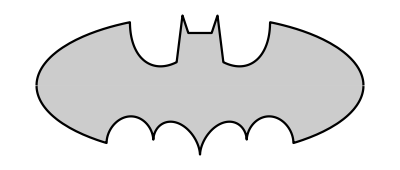

```mathematica
Plot[{With[{w=3*Sqrt[1-(x/7)^2],l=(6/7)*Sqrt[10]+(3+x)/2-(3/7)*Sqrt[10]*Sqrt[4-(x+1)^2],h=(1/2)*(3*(Abs[x-1/2]+Abs[x+1/2]+6)-11*(Abs[x-3/4]+Abs[x+3/4])),r=(6/7)*Sqrt[10]+(3-x)/2-(3/7)*Sqrt[10]*Sqrt[4-(x-1)^2]},w+(l-w)*UnitStep[x+3]+(h-l)*UnitStep[x+1]+(r-h)*UnitStep[x-1]+(w-r)*UnitStep[x-3]],(1/2)*(3*Sqrt[1-(x/7)^2]+Sqrt[1-(Abs[Abs[x]-2]-1)^2]+Abs[x/2]-((3*Sqrt[33]-7)/112)*x^2-3)*((x+4)/Abs[x+4]-(x-4)/Abs[x-4])-3*Sqrt[1-(x/7)^2]},{x,-7,7},AspectRatio->Automatic,PlotStyle->Black,Axes->False,Filling->Axis]
```